```mathematica
<<"/home/farmer/mathematica/DMFormFactor_13086288/v6/dmformfactor-V6.m"
Xe131filename="default";
bFM="default";SetIsotope[54,131,bFM,Xe131filename];ve=232 KilometerPerSecond;
v0=220 KilometerPerSecond;
vesc=550 KilometerPerSecond;
SetHALO["MBcutoff"];
mNucleon=0.938 GeV;
NT=1/(131 mNucleon);
Centimeter=(10^13 Femtometer);
rhoDM=0.3 GeV/Centimeter^3;
(*from here change for your settings*)
SetJChi[1/2];
SetMChi[500 GeV]
ZeroCoeffs[]
SetCoeffsNonrel[7,50,0]
myrate[qGeV_]=(7200 KilogramDay) EventRate[NT,rhoDM,qGeV,ve,v0,vesc];
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

Getting default matrix...

Setting isotope to xenon-131.

Your Lagrangian is

L_prot=0.+(0.000412443 S_N·v^⊥)/GeV^2

L_neut=0.+(0.000412443 S_N·v^⊥)/GeV^2

Your event rate is

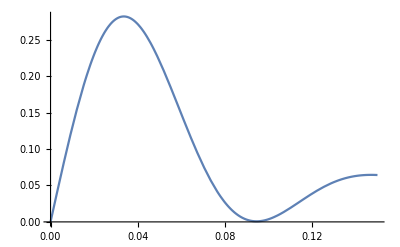

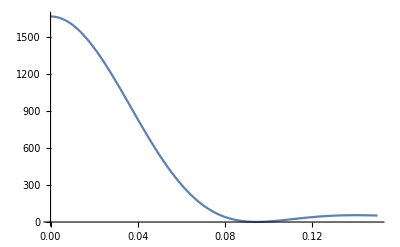

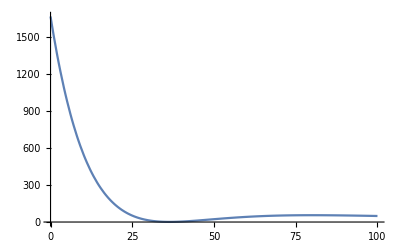

```mathematica
plot=Plot[myrate[qGeV] GeV*(qGeV GeV/(131 mNucleon)),{qGeV,0,0.15},PlotRange->All]
plot=Plot[myrate[qGeV] GeV,{qGeV,0,0.15},PlotRange->All]
plot=Plot[myrate[qGeV] GeV/.qGeV->√(10^-6*2mT ER/GeV),{ER,0,100},PlotRange->All]
```